```mathematica
ClearAll["Global`*"];
(*Lecący poziomo pocisk z prędkością vₚ, o masie m, utkwił w klocku
o masie M=10 kg. Sporządzić wykresy:
a) zależności prędkości początkowej klocka z pociskiem od prędkości pocisku
b) zależności ciepła wydzielonego w zderzeniu od prędkości pocisku
c) zależności drogi, jaką przebędzie klocek z pociskiem po płaszczyźnie poziomej, od prędkości pocisku,jeżeli współczynnik tarcia k=0,1.
Wszystkie wykresy sporządzić dla vₚ=50÷100 m/s
dla dwóch mas pocisków: m=10 g oraz m=15 g.*)
```

```mathematica
rown1=Solve[m×vp==(m+M)×vpk,vpk]
```

{{vpk→(m vp)/(m+M)}}

```mathematica
vpk=vpk/.rown1[[1]]
```

(m vp)/(m+M)

```mathematica
Ekp=(m×vp^2)/2;
Ekpk=((m+M)×vpk^2)/2;
```

```mathematica
Q=Ekp-Ekpk
```

(m vp^2)/2-(m^2 vp^2)/(2 (m+M))

```mathematica
M=10; (* kg *)
```

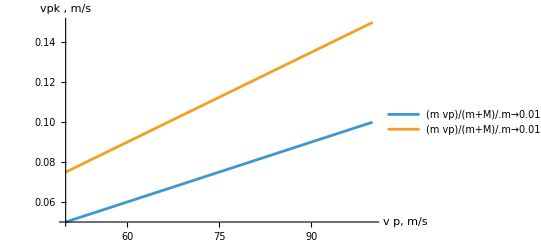

```mathematica
rys1=Plot[{vpk/.m->0.01,vpk/.m->0.015},{vp,50,100},AxesLabel->{"v p, m/s ","vpk , m/s"},PlotLegends->"Expressions"]
```

### .

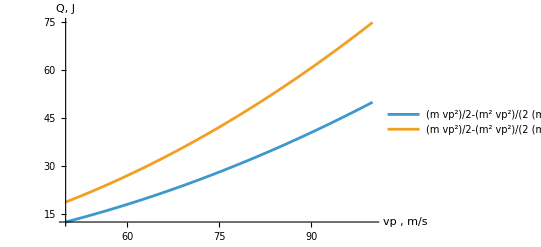

```mathematica
rys2=Plot[{Q/.m->0.01,Q/.m->0.015},{vp,50,100},AxesLabel->{"vp , m/s ","Q, J"},PlotLegends->"Expressions"]
```

```mathematica
g=9.81 ;(* m/s^2 *)
k=0.1 ; (* 1 *)
```

```mathematica
WT=(m+M)×g×k×Lpoz;
```

```mathematica
rown2=Solve[WT==Ekpk,Lpoz]
```

{{Lpoz→(0.509684 m^2 vp^2)/(10.+m)^2}}

```mathematica
Lpoz=Lpoz/.rown2[[1]]
```

(0.509684 m^2 vp^2)/(10.+m)^2

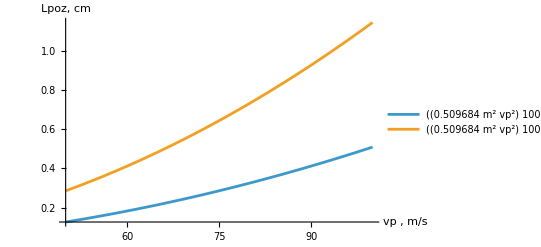

```mathematica
rys2=Plot[{Lpoz×100/.m->0.01,Lpoz×100/.m->0.015},{vp,50,100},AxesLabel->{"vp , m/s ","Lpoz, cm"},PlotLegends->"Expressions"]
```